# Parcialne diferencialne enačbe (2. del)

## Laplaceova enačba v polarnih koordinatah

Ukaza, ki jih bomo uporabili za grafični prikaz rešitve.

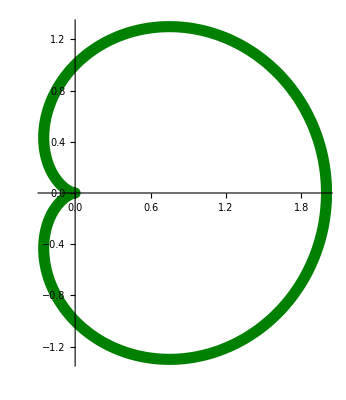

```mathematica
PolarPlot[1+Cos[φ],{φ,0,2π},PlotStyle->Thickness[0.02],ColorFunction->Function[{x,y,φ,r},RGBColor[0,φ/(2π),0]],
ColorFunctionScaling->False]
```

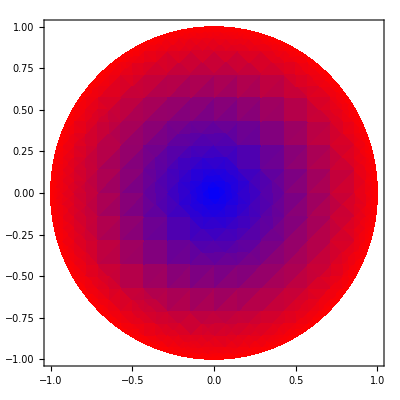

```mathematica
u[r_,φ_]=r;
r=√(x^2+y^2);
φ=ArcTan[x,y];
DensityPlot[u[r,φ] ,
{x,-1,1},{y,-1,1},
ColorFunction->Function[{u},RGBColor[u,0,1-u]],
RegionFunction->Function[{x,y},√(x^2+y^2)<1],
ColorFunctionScaling->False
]
```

V polarnih koordinatah se Δu = 0 prevede do
               u_rr+u_r/r+u_φφ/r^2=0

1. korak: Separacija spremenljivk

Δ u=u_rr+u_r/r+u_φφ/r^2
     u[r,φ]=R[r]F[φ]
     -(r^2 R''[r]+r R'[r])/R[r]=F''[φ]/F[φ]=-k^2

     F''[φ]+k^2 F[φ]=0
     r^2 R''[r]+r R'[r]-k^2 R[r]=0          (Eulerjeva diferencialna enačba)

2. korak: Rešiti obe diferencialni enačbi - rešitve F(φ) morajo imeti periodo 2π.

F_k[φ]=A_k Cos[k φ]+B_k Sin[k φ]   konstanta k=0 je tukaj skrita
     F_k[φ+2π]=F_k[φ]   za     k=0,1,2...
     F_k[φ]=A_k Cos[k φ]+B_k Sin[k φ]

     R_k[r]=C_k r^k+D_k r^-k
     R_0[r]=C_0+D_0 Log[r]

3. korak (superpozicija) to je to ne rabiš zmer izpeljevat

u[r,φ]=C_0+D_0 Log[r]+ ∑_(k=1)^∞ (A_k Cos[k φ]+B_k Sin[k φ])(C_k r^k+D_k r^-k)

### Dirichletova naloga za notranjost kroga

Δu = 0, za vse r < a     (a je radij kroga)
               u(0,φ) < ∞     mora biti definirana.
               u(a,φ) = f(φ)     na krožnici je neka funkcija fi-ja.

4. korak: Zadostiti treba vrednostim na robu kroga

u[0,φ] mora biti definiran ... sledi...  D_k=D_0=0   vedno ko smo v notranjosti kroga!!!
     u[r,φ]=A_0+∑_(k=1)^∞ (A_k Cos[k φ]+B_k Sin[k φ])r^k
     u[a,φ]=f[φ]=A_0+∑_(k=1)^∞ (A_k Cos[k φ]+B_k Sin[k φ])a^k ... sledi...
     A_0,A_k a^k in B_k a^k so koeficienti v razvoju funkcije f[φ] v Fourierovo vrsto na intervalu (-π,π)


Če smo na zunanjosti je Ck enak nič! in je potem a^-k

Podatki:

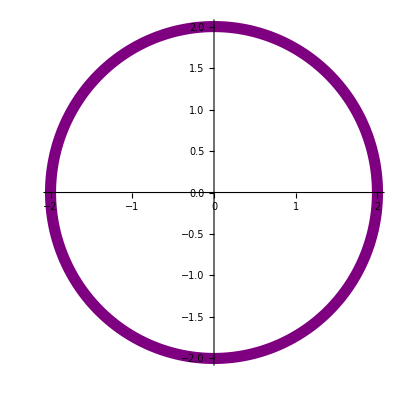

```mathematica
Clear[a,u,r,φ,f]
a=2;
f1[φ_]=Piecewise[{{1,0<φ<π},{0,-π<φ<0}}];
f2[φ_]=If[φ>π/4 && φ<3π/4,1,0];
f3[φ_]=(1+Sin[4φ])/2;
f[φ_]=f3[φ];
PolarPlot[a,{φ,0,2π},PlotStyle->Thickness[0.02],ColorFunction->Function[{x,y,φ,r},RGBColor[f[φ],0,1-f[φ]]],
ColorFunctionScaling->False]
```

Rešitev:

0.5+r^4 (0.+0.03125 Sin[4 φ])

-Graphics-

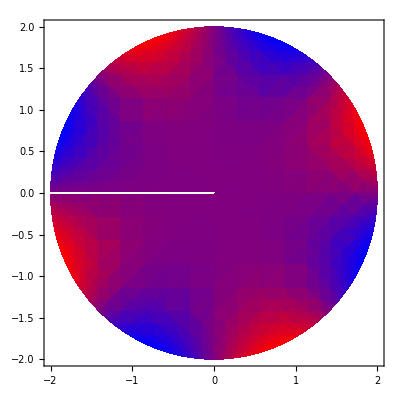

```mathematica
Clear[r,φ,u]
M=5;
A0=(1/(2π))Integrate[f[φ],{φ,-π,π}];
A=Table[(1/π)Integrate[f[φ]Cos[k φ],{φ,-π,π}]/a^k,{k,1,M}]//N;
B=Table[(1/π)Integrate[f[φ]Sin[k φ],{φ,-π,π}]/a^k,{k,1,M}]//N;
u[r_,φ_]=A0+Sum[(A_⟦k⟧Cos[k φ]+B_⟦k⟧Sin[k φ])r^k,{k,1,M}]

(* Vrednost rešitve na robu kroga *)
PolarPlot[a,{φ,0,2π},PlotStyle->Thickness[0.02],ColorFunction->Function[{x,y,φ,r},RGBColor[u[a,φ],0,1-u[a,φ]]],
ColorFunctionScaling->False]

(* Rešitev v notranjosti *)
r=√(x^2+y^2);
φ=ArcTan[x,y];
DensityPlot[u[r,φ],
{x,-a,a},{y,-a,a},
ColorFunction->Function[{u},RGBColor[u,0,1-u]],
RegionFunction->Function[{x,y},√(x^2+y^2)<a],
ColorFunctionScaling->False
]
```

### Dirichletova naloga za kolobar

Δu = 0, kjer q < r < Q        q Q sta robova
               u(q ,φ ) = f(φ )
               u(Q,φ ) = F(φ )

4. korak: Zadostiti treba vrednostim na robu kolobarja

u[r,φ]=(C_0+D_0 Log[r])+∑_(k=1)^∞ ( C_k r^k+ D_k r^-k)(A_k Cos[k φ]+B_k Sin[k φ])

     u[r,φ]=(α_0+γ_0 Log[r])+∑_(k=1)^∞ (α_k r^k+γ_k r^-k)Cos[k φ]+(β_k r^k+δ_k r^-k)Sin[k φ]
Vstavimo notranji in zunanji radij:
     u[q,φ]=(α_0+γ_0 Log[q])+∑_(k=1)^∞ (α_k q^k+γ_k q^-k)Cos[k φ]+(β_k q^k+δ_k q^-k)Sin[k φ]
     u[Q,φ]=(α_0+γ_0 Log[Q])+∑_(k=1)^∞ (α_k Q^k+γ_k Q^-k)Cos[k φ]+(β_k Q^k+δ_k Q^-k)Sin[k φ]
Razvijemo funkciji iz podatkov v Fourierovi vrsti:
     f[φ]=a_0+∑_(k=1)^∞ (a_k Cos[k φ]+b_k Sin[k φ])
     F[φ]=A_0+∑_(k=1)^∞ (A_k Cos[k φ]+B_k Sin[k φ])
in za vsak indeks  k  s primerjavo določimo neznane koeficiente
     α_k, β_k, γ_k, δ_k


sistem enačb- več manjših ststemov.

Podatki

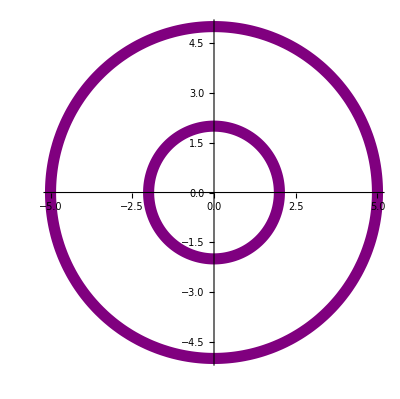

```mathematica
Clear[r,φ,f]
q=2;
Q=5;
(* primeri različnih podatkov *)
f1[φ_]=1; F1[φ_]=0;
f2[φ_]=Abs[φ/π]; F2[φ_]=1-Abs[φ/π];
(* izbrani funkciji f in F *)
f[φ_]=f2[φ];  F[φ_]=F2[φ];
PolarPlot[{q,Q},{φ,-π,π},PlotStyle->Thickness[0.02],
ColorFunction->Function[{x,y,φ,r},RGBColor[ If[r>q,F[φ],f[φ]] ,0,1-If[r>q,F[φ],f[φ]]]],
ColorFunctionScaling->False]
```

Rešitev

```mathematica
Clear[r,φ]
M=3;

(* Določitev koeficientov  Subscript[α, k],Subscript[β, k],Subscript[γ, k],Subscript[δ, k]  za indekse  k=1,2,3,...
   Rezultat so seznami koeficientov α,β,γ,δ *)
For[α=β=γ=δ={};k=1,k≤M,k++,
s=Solve[{
αk q^k+γk q^-k==N[(1/π)Integrate[f[φ]Cos[k φ],{φ,-π,π}]],
αk Q^k+γk Q^-k==N[(1/π)Integrate[F[φ]Cos[k φ],{φ,-π,π}]],
βk q^k+δk q^-k==N[(1/π)Integrate[f[φ]Sin[k φ],{φ,-π,π}]],
βk Q^k+δk Q^-k==N[(1/π)Integrate[F[φ]Sin[k φ],{φ,-π,π}]]},{αk,βk,γk,δk}];
AppendTo[α,αk/. s_⟦1⟧];
AppendTo[β,βk/. s_⟦1⟧];
AppendTo[γ,γk/. s_⟦1⟧];
AppendTo[δ,δk/. s_⟦1⟧]; ]
(* Določitev koeficientov  Subscript[α, 0],Subscript[β, 0]  za indeks k=0 *)
s=Solve[{
α0+γ0 Log[q]==N[(1/(2π))Integrate[f[φ],{φ,-π,π}]],
α0+γ0 Log[Q]==N[(1/(2π))Integrate[F[φ],{φ,-π,π}]]},{α0,γ0}];

(* Rešitev naloge *)
u[r_,φ_]:=(α0+γ0 Log[r])+∑_(k=1)^M ((α_⟦k⟧r^k+γ_⟦k⟧r^-k)Cos[k φ]+(β_⟦k⟧r^k+δ_⟦k⟧r^-k)Sin[k φ])/. s_⟦1⟧
```

```mathematica
(* Vrednost rešitve na robu kolobarja *)
PolarPlot[{q,Q},{φ,-π,π},PlotStyle->Thickness[0.02],
ColorFunction->Function[{x,y,φ,r},RGBColor[ u[If[r>q,Q,q],φ] ,0,1-u[If[r>q,Q,q],φ]]],
ColorFunctionScaling->False]
```

-Graphics-

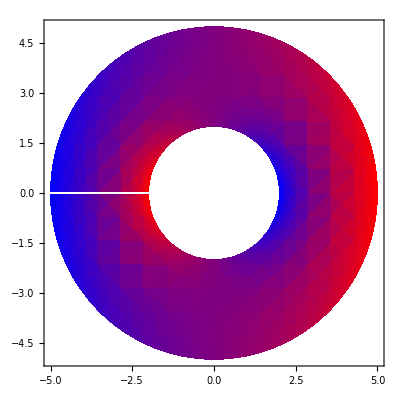

```mathematica
(* Rešitev v notranjosti kolobarja *)
r=√(x^2+y^2);
φ=ArcTan[x,y];
DensityPlot[u[r,φ],
{x,-Q,Q},{y,-Q,Q},
ColorFunction->Function[{u},RGBColor[u,0,1-u]],
RegionFunction->Function[{x,y},q<√(x^2+y^2)<Q]
]
```

### Primeri nalog za preverjanje

1. V polarnih koordinatah je rešitev Laplaceove parcialne diferencialne enačbe  Δu(r,φ)=0  funkcija
               u[r,φ]=A0+B0 Log[r]+∑_(n=1)^∞ ( a[n]r^n+b[n]r^-n ) (A[n] Cos[n φ]+B[n] Sin[n φ])
     Določite koeficiente v rešitvi Dirichletove naloge za notranjost kroga
               Δu(r,φ)=0,kjer r<2
               u(2,φ)={ π-|π-2φ| | , če
0 | , če    0< φ < π
-π≤ φ ≤ 0 

     Približno koliko je  u(1,2), če upoštevamo prvih 5 členov Fourierove vrste (do indeksa n=5)?

Rezultat: 1.47238

```mathematica
Clear[A0,B0,A,B,a,b,u,r,φ ]
u[r_,φ_]=A0+B0 Log[r]+∑_(n=1)^∞ ( a[n] r^n+b[n] r^-n ) (A[n] Cos[n φ]+B[n] Sin[n φ]) /.{B0->0,b[n]-> 0,a[n]-> 1}

(*ker smo na krogu, lahko postavimo B0 in b na nič in celo a na 1*)
f=If[0< φ < π, π-Abs[π-2φ],0]
u[2,φ]==f(*Dobimo four vi+rsto na (-pi,pi). Pazi na koeficiente saj vsebujejo tudi 2^n*)


A0= 1/(2Pi)Integrate[f,{φ,-Pi,Pi}]
A[n_]=1/Pi Integrate[f Cos[n φ],{φ,-Pi,Pi}]/2^n
B[n_]=1/Pi Integrate[f Sin[n φ],{φ,-Pi,Pi}]/2^n
U[r_,φ_]= A0 +  Sum[r^n(A[n] Cos[n φ]+ B[n] Sin[n φ]), {n,1,5}]
u[1,2]//N
```

A0+∑_(n=1)^∞ r^n (A[n] Cos[n φ]+B[n] Sin[n φ])

If[0<φ<π,π-Abs[π-2 φ],0]

A0+∑_(n=1)^∞ 2^n (A[n] Cos[n φ]+B[n] Sin[n φ])==If[0<φ<π,π-Abs[π-2 φ],0]

π/4

(2^(1-n) (-1+2 Cos[(n π)/2]-Cos[n π]))/(n^2 π)

(2^(1-n) (2 Sin[(n π)/2]-Sin[n π]))/(n^2 π)

π/4-(r^2 Cos[2 φ])/(2 π)+(2 r Sin[φ])/π-(r^3 Sin[3 φ])/(18 π)+(r^5 Sin[5 φ])/(200 π)

1.47122+0. ⅈ

2. V polarnih koordinatah je rešitev Laplaceove  parcialne diferencialne enačbe  Δu(r,φ)=0  funkcija
               u[r,φ]=A0+B0 Log[r]+∑_(n=1)^∞ ( a[n]r^n+b[n]r^-n ) (A[n] Cos[n φ]+B[n] Sin[n φ])
     Določite koeficiente v rešitvi Dirichletove naloge za zunanjost kroga
               Δu(r,φ)=0, kjer r>2
               u(2,φ)={ π-|π-2φ| | , če
0 | , če    0< φ < π
-π≤ φ ≤ 0 
               lim_(r→∞)  u(r,φ)=0

     Približno koliko je u(4,1), če upoštevamo prvih 5 členov Fourierove vrste (do indeksa n=5)?

Rezultat: 1.38331

```mathematica
Clear[A0,B0,A,B,a,b,u,r,φ ]
u[r_,φ_]=A0+B0 Log[r]+∑_(n=1)^∞ ( a[n] r^n+b[n] r^-n ) (A[n] Cos[n φ]+B[n] Sin[n φ]) /.{B0->0,b[n]-> 1,a[n]-> 0}

(*ker smo na krogu, lahko postavimo B0 in a na nič in celo b na 1*)
f=If[0< φ < π, π-Abs[π-2φ],0]
u[2,φ]==f(*Dobimo four vi+rsto na (-pi,pi). Pazi na koeficiente saj vsebujejo tudi 2^n*)


A0= 1/(2Pi)Integrate[f,{φ,-Pi,Pi}]
A[n_]=1/Pi Integrate[f Cos[n φ],{φ,-Pi,Pi}]/2^(-n )(*Sprememba*)
B[n_]=1/Pi Integrate[f Sin[n φ],{φ,-Pi,Pi}]/2^(-n)
U[r_,φ_]= A0 +  Sum[r^(-n)(A[n] Cos[n φ]+ B[n] Sin[n φ]), {n,1,5}]
u[4,1]//N
```

A0+∑_(n=1)^∞ r^-n (A[n] Cos[n φ]+B[n] Sin[n φ])

If[0<φ<π,π-Abs[π-2 φ],0]

A0+∑_(n=1)^∞ 2^-n (A[n] Cos[n φ]+B[n] Sin[n φ])==If[0<φ<π,π-Abs[π-2 φ],0]

π/4

(2^(1+n) (-1+2 Cos[(n π)/2]-Cos[n π]))/(n^2 π)

(2^(1+n) (2 Sin[(n π)/2]-Sin[n π]))/(n^2 π)

π/4-(8 Cos[2 φ])/(π r^2)+(8 Sin[φ])/(π r)-(32 Sin[3 φ])/(9 π r^3)+(128 Sin[5 φ])/(25 π r^5)

1.38215+0. ⅈ

3. Poiščite tisto rešitev u(r,φ)parcialne diferencialne enačbe
               Δu(r,φ)=0,   kjer  1<r<3
               u(1,φ)=4,
               u(3,φ)=8,
     ki je neodvisna od kota φ.
     Koliko je u(2,φ)?
     
     Pomoč: Laplaceov operator v polarnih koordinatah je
               Δu= u_rr+1/r u_r+1/r^2 u_φφ

Rezultat: 6.52372

```mathematica
(*Ker iščemo rešitev ki je neodvisna od fi se vsi členi ki vsebujejo parcialni odvod po fi enaki 0. In nam ostane samo navadna DE za r*)
Clear[u]
DSolve[{u''[r]+1/r u'[r]==0, u[1]==4, u[3]==8}, u[r],r]
%/. r->2//N
```

{{u[r]→(4 (Log[3]+Log[r]))/Log[3]}}

{{u[2.]→6.52372}}

4. Poiščite tisto rešitev u(r,φ,θ)parcialne diferencialne enačbe
               Δu(r,φ,θ)=0 ,  kjer  3<r<5
               u(3,φ,θ)=3
               u(5,φ,θ)=5,
     ki je neodvisna od kotov φ in θ.
     Koliko je  u(4,φ,θ)?
     
     Pomoč: Laplaceov operator v sferičnih koordinatah je
     Δu= u_rr+2/r u_r+1/r^2 u_φφ+(ctg φ)/r^2 u_φ+1/(r^2 sin^2 φ)u_θθ

Rezultat: 4.25

```mathematica
Clear[u]
DSolve[{u''[r]+2/ r u'[r]==0, u[3]==3, u[5]==5}, u[r],r]
%/. r->4//N
```

{{u[r]→(-15+8 r)/r}}

{{u[4.]→4.25}}